```mathematica
SetDirectory[NotebookDirectory[]] ;
```

```mathematica
data = Import["solution.dat"];
norms= (Import["norms.dat"])[[1,3;;]];
Length@data
```

13

```mathematica
func=Table[norms[[i]]/norms[[1]],{i,1,Length@norms}];
```

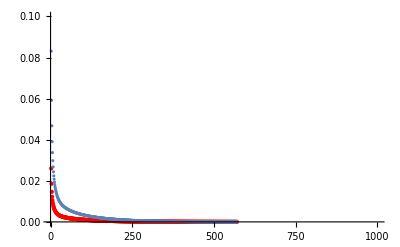

```mathematica
Show[ListPlot[norms,PlotStyle->Red,PlotRange->{{0,1000},{0,0.1}}],ListPlot[func,PlotRange->{{0,1000},{0,0.1}}]]
```

```mathematica
makeDataT[data_]:=Module[{N0,L0,N1,L1,h1,h2,x1,x2,d,res},
{N0,L0} = data[[-2]];
{N1,L1} = data[[-1]];
{h1,h2} = {L0/N0,L1/N1};
x1 = Table[i * h1, {i,0,N0}];
x2 = Table[i * h2, {i,0,N1}];
d= data[[;;-3]];
res=Flatten[Table[Table[{x1[[j]],x2[[i]],d[[i,j]]},{i,1,N1 +1 }],{j,1,N0 + 1}],1];res = DeleteCases[res,{0,0,_}];
res = DeleteCases[res,{0,1,_}];
res = DeleteCases[res,{1,0,_}];
 DeleteCases[res,{1,1,_}]
];
```

```mathematica
dataT = makeDataT[data];
```

```mathematica
s[x_,y_]:=x^2+y^2 ;
```

```mathematica
Show[Plot3D[s[x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap",AxesLabel->{"x1","x2","T"}],ListPlot3D[dataT,ColorFunction->"TemperatureMap",PlotRange->Full,AxesLabel->{"x1","x2","T"}]]
```

-Graphics3D-

```mathematica
dataMIS = {#[[1]],#[[2]],Abs[#[[3]]-s[#[[1]],#[[2]]]]}&/@dataT;
```

```mathematica
ListPlot3D[dataMIS,ColorFunction->"TemperatureMap",PlotRange->Full,AxesLabel->{"x1","x2","T"}]
```

-Graphics3D-

### Порядок аппроксимации

```mathematica
G=s;
```

```mathematica
(*MaxNorm[numsol_,realsol_]:=Module[{},
Return[Max[Table[Max[numsol[[i]]-realsol[[i]]],{i,1,Length@realsol}]]];
];
NormS[numsol_,func_,t_,m_,h_]:=Module[{sol,n = Length@(numsol[[1]])},
sol=Table[Table[G[i*h,j*t],{i,0,n-1}],{j,0,m }];
Return[Max[Table[MaxNorm[numsol[[i]],sol[[i]]],{i,1,Length@numsol}]]];
];*)
NormLOL[sol_,G_]:=Max[Table[Abs[sol[[i,3]]-G[sol[[i,1]],sol[[i,2]]]],{i,1,Length@sol}]];
```

```mathematica
data1x1t = makeDataT@Import["solution_1x1y.dat"];
data1x2t  =makeDataT@Import["solution_1x2y.dat"];
data1x3t  =makeDataT@ Import["solution_1x3y.dat"];
data2x1t  = makeDataT@Import["solution_2x1y.dat"];
data2x2t  = makeDataT@Import["solution_2x2y.dat"];
data2x3t  = makeDataT@Import["solution_2x3y.dat"];
data3x1t  =makeDataT@ Import["solution_3x1y.dat"];
data3x2t  = makeDataT@Import["solution_3x2y.dat"];
data3x3t  = makeDataT@Import["solution_3x3y.dat"];
A={{NormLOL[data1x1t,G],NormLOL[data2x1t,G],NormLOL[data3x1t,G]},
{NormLOL[data1x2t,G],NormLOL[data2x2t,G],NormLOL[data3x2t,G]},
{NormLOL[data1x3t,G],NormLOL[data2x3t,G],NormLOL[data3x3t,G]}};
```

```mathematica
howmuch=3;
n = 5; m = 5;
```

```mathematica
H = {1/n, 1/(2n),1/(4n)};
TAU ={1/m, 1/(2m),1/(4m)};
HtauGrid=Table[Table[0,{i,1,2*howmuch}],{j,1,2*howmuch}];
For[i =2,i ≤ Length@HtauGrid,i+=2, 
HtauGrid[[i,1]]=H[[i/2]]//N;
For[j =2,j ≤ Length@HtauGrid,j+=2,
HtauGrid[[1,j]]=TAU[[j/2]]//N;
HtauGrid[[i,j]]=A[[j/2,i/2]];
];
];
HtauGrid[[1,1]]="h1 \\\ h2";

For[i=3,i<Length@HtauGrid+1,i+=2,
For[j=1,j<Length@HtauGrid+1,++j,
If[(OddQ[j]≠ True||j==1),
HtauGrid[[i,j]]=HtauGrid[[i-1,j]]/HtauGrid[[i+1,j]]"↓";
HtauGrid[[j,i]]=HtauGrid[[j,i-1]]/HtauGrid[[j,i+1]]"→",
HtauGrid[[i,j]]=HtauGrid[[i-1,j-1]]/HtauGrid[[i+1,j+1]]"↘";
HtauGrid[[j,i]]=HtauGrid[[j-1,i-1]]/HtauGrid[[j+1,i+1]]"↘";
];
];
];
style=Flatten[Table[Table[{i,j}->Red,{i,2,6,2}],{j,2,6,2}],1];
Grid[HtauGrid,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->{Automatic,Automatic,style}]
```

h1 \ h2 | 0.2 | 2. → | 0.1 | 2. → | 0.05
0.2 | 0.135137 | 0.998707 → | 0.135312 | 0.994407 → | 0.136073
2. ↓ | 2.34125 ↓ | 2.32923 ↘ | 2.33224 ↓ | 2.31893 ↘ | 2.33197 ↓
0.1 | 0.05772 | 0.994864 → | 0.058018 | 0.994293 → | 0.058351
2. ↓ | 2.25848 ↓ | 2.24504 ↘ | 2.25663 ↓ | 2.24103 ↘ | 2.25389 ↓
0.05 | 0.025557 | 0.994049 → | 0.02571 | 0.993086 → | 0.025889

```mathematica
datat =  makeDataT@Import["solution 2x.dat"];
```

```mathematica
NormLOL[dataT,G]/NormLOL[datat,G]
```

2.14381